### Numerical integration using MonteCarlo integration: Convert an integration problem into a sampling problem

Using mean value theorem of integration,  ∫_xMin^xMax f(x)ⅆx is given by f(c)(xMax - xMin) where f(c) is the “area of the curve”.  The function f(c) can be estimated by choosing random variables x\[Distributed]UniformDistribution[{xMin,xMax}].  The f(c), which is an average height of the function f(x) is then calculated as the expectation of the function f(x) when  is chosen randomly from a uniform distribution between xMin and xMax

Example problem: Integrate f(x)  = Cos(x) between the limits -3.5 and 3.5 using the Monte Carlo method.  Compare with analytical method

```mathematica
mcIntegrate[xMin_,xMax_,f_]:=Module[{xMin1=xMin, xMax1=xMax,f1=f},
NExpectation[f,x\[Distributed]UniformDistribution[{xMin,xMax}],Method->"MonteCarlo",AccuracyGoal->5]*(xMax-xMin)
]
```

```mathematica
mcIntegrate[-3.5,3.5,Cos[x]]
```

-0.702417

"Analytical" solution and L-2 (Frobenius) norm of error

```mathematica
{Integrate[ Cos[x],x], iExact=Integrate[Cos[x],{x,-3.5,3.5}],Norm[mcIntegrate[-3.5,3.5,Cos[x]]-iExact,"Frobenius"]}
```

{Sin[x],-0.701566,0.00126258}

```mathematica
NIntegrate[Cos[x],{x,-3.5,3.5},Method->"MonteCarlo"]//Quiet
```

-0.703549

### Solve a differential equation by applying the Monte Carlo integration method

Example problem: Solve (∂u)/(∂x)==x with the initial condition u(x_0) = 1

This problem may be solved analytically as u(x) =u(x_0) + ∫_x_0^ξ xⅆx.  The integral, ∫_x_0^ξ xⅆx, may be performed using the Monte Carlo method

```mathematica
u0 = 1; (*Initial condition*)
uMC=u0 + mcIntegrate[0,ξ,x]
```

1+ξ NExpectation[x,x\[Distributed]UniformDistribution[{0,ξ}],Method→MonteCarlo,AccuracyGoal→5]

The exact solution is easily found as a function of x.  One can substitute a desired value for x to evaluate the solution at that location.

```mathematica
uExact=DSolveValue[{u'[x]==x,u[0]==1},u[x],x]
```

1/2 (2+x^2)

Comparison of "Exact" solution vs Monte Carlo solution for x=5

```mathematica
{uMC/.ξ->5, uExact/.x->5//N}
```

{13.4974,13.5}

#### This integration may also be completed through the MonteCarlo setting in NIntegrate

```mathematica
NIntegrate[Cos[x],{x,-3.5,3.5},Method->"Trapezoidal"]
NIntegrate[Cos[x],{x,-3.5,3.5},Method->"MonteCarlo"]//Quiet
```

-0.701566

-0.715169

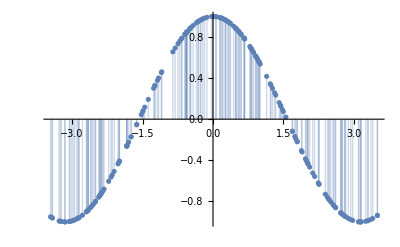

```mathematica
ListPlot[Last[Reap[NIntegrate[Cos[x],{x,-3.5,3.5},Method->"MonteCarlo",MaxPoints->100,EvaluationMonitor:>Sow[{x,Cos[x]}]]]],Filling->0,AxesOrigin->{0,0}]//Quiet
```